```mathematica
Clear[I0]
r0=340;
```

```mathematica
ρ[r_,w_]=(2 (r)^2)/w^2;
Intensity[I0_,r_,w_,θ_,p_,l_]=I0*(ρ[r,w])^l*(LaguerreL[p,l,ρ[r,w]])^2(Cos[l*θ])^2 Exp[-ρ[r,w]];
(*See Koechner p. 211 (225)*)
IntensityHer[I0_,x_,w_,y_,p_,l_]=I0*(HermiteH[p,x*Sqrt[2]/w]*Exp[-x^2/w^2]*HermiteH[l,y*Sqrt[2]/w]*Exp[-y^2/w^2])^2;
```

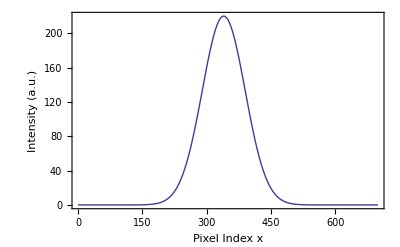

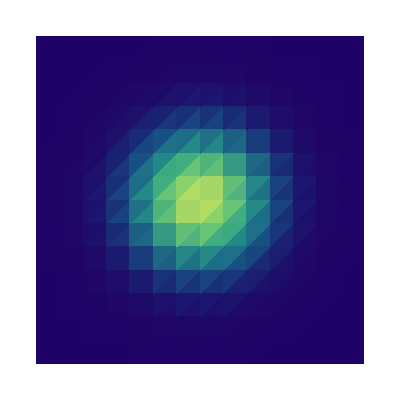

```mathematica
n=0;
m=0;
Plot[Intensity[220,(x-r0),100,0,n,m],{x,0,700},PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{{"Intensity (a.u.)","Intensity (a.u.)"},{"Pixel Index x","Pixel Index x"}}]
DensityPlot[Intensity[1,(x^2+y^2)^0.5,5,ArcTan[y/x],n,m],{x,-10,10},{y,-10,10},Frame->False,Axes->False,ColorFunction->"BlueGreenYellow",PlotRange->All]
```

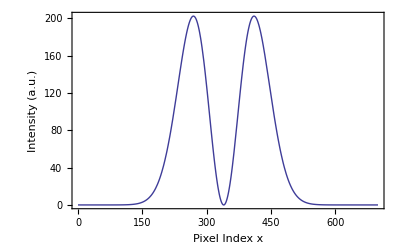

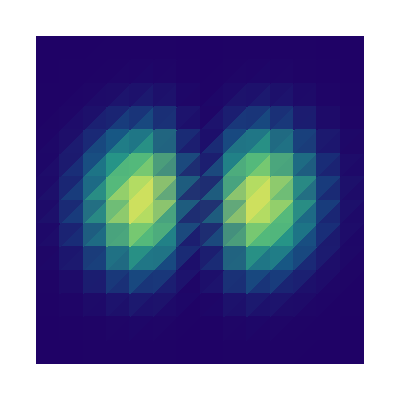

```mathematica
n2=0;
m2=1;
Plot[Intensity[550,(x-r0),100,0,n2,m2],{x,0,700},PlotRange->Automatic,Frame->{{True,False},{True,False}},FrameLabel->{{"Intensity (a.u.)","Intensity (a.u.)"},{"Pixel Index x","Pixel Index x"}}]
DensityPlot[Intensity[1,(x^2+y^2)^0.5,5,ArcTan[y/x],n2,m2],{x,-10,10},{y,-10,10},Frame->False,Axes->False,ColorFunction->"BlueGreenYellow"]
```

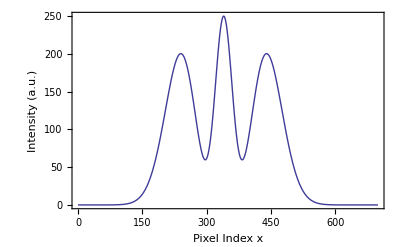

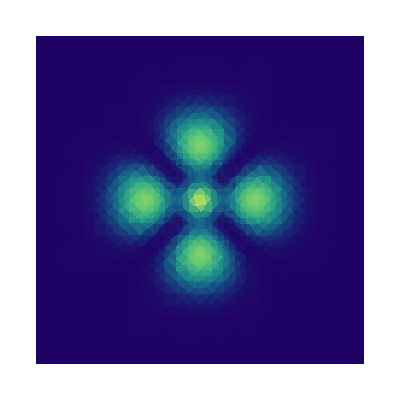

```mathematica
n3=0;
m3=2;
n0=0;
m0=0;
Plot[Intensity[370,(x-r0),100,0,n3,m3]+Intensity[250,(x-r0),40,0,n0,m0],{x,0,700},PlotRange->Automatic,Frame->{{True,False},{True,False}},FrameLabel->{{"Intensity (a.u.)","Intensity (a.u.)"},{"Pixel Index x","Pixel Index x"}}]
DensityPlot[Intensity[370,(x^2+y^2)^0.5,100,ArcTan[y/x],n3,m3]+Intensity[250,(x^2+y^2)^0.5,40,ArcTan[y/x],n0,m0],{x,-300,300},{y,-300,300},Frame->False,Axes->False,ColorFunction->"BlueGreenYellow",PlotRange->All]
```

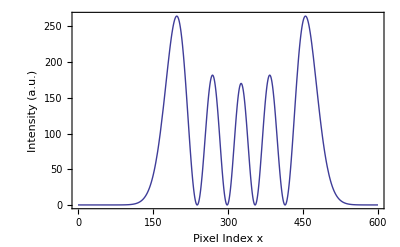

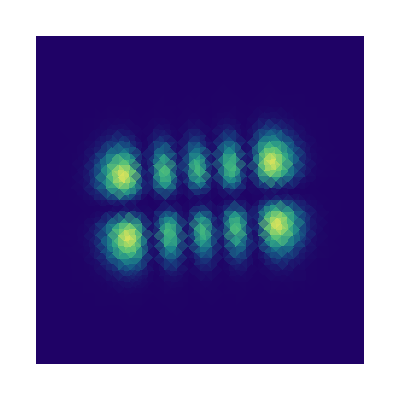

```mathematica
n4=4;
m4=1;
Plot[IntensityHer[4,(x-300)*Cos[-5Degree]-(0-300)*Sin[-5Degree],75,15,n4,m4],{x,0,600},PlotRange->Automatic,Frame->{{True,False},{True,False}},FrameLabel->{{"Intensity (a.u.)","Intensity (a.u.)"},{"Pixel Index x","Pixel Index x"}}]
DensityPlot[IntensityHer[2,(x-300)*Cos[-5Degree]-(y-300)*Sin[-5Degree],80,(x-300)*Sin[-5Degree]+(y-300)*Cos[-5Degree],n4,m4],{x,0,600},{y,0,600},Frame->False,Axes->False,ColorFunction->"BlueGreenYellow",PlotRange->All]
```